## Basic CR model

### Initialize constants

Set number of consumers, resources, and enzyme budget

```mathematica
m=4;
p=3;
enzymeBudget=1;
```

Define constants for each consumer

```mathematica
c=enzymeBudget*Normalize[#,Total]&/@RandomReal[{0,1},{m,p}];(*preference vector for each species*)
g=Table[1,m,p](*metabolic conversion coefficient for each resource*);
z=Table[0.1,m](*loss function/death for each species*);
```

Define constants for each resource

```mathematica
κ=Table[0.3,p];
μ=Table[0,p];
```

### Initialize populations

```mathematica
r0=Table[1,p];
n0=Table[1,m];
```

### Solve The differential equations

```mathematica
sols=NDSolve[{
r[0]==r0,
r'[t]==κ-μ*r[t]-r[t]*n[t].c,
n[0]==n0,
n'[t]==n[t]*(r[t].Transpose[c*g]-z)
},
{r,n},
{t,0,10000}][[1]];
```

### Plot dynamics

```mathematica
sols
```

{r→InterpolatingFunction[…],n→InterpolatingFunction[…]}

```mathematica
Show[Plot3D[1-x-y,{x,0,1},{y,0,1},PlotStyle->Directive[Opacity[0.3]]],ListPointPlot3D[List/@c],AspectRatio->1]
```

-Graphics3D-

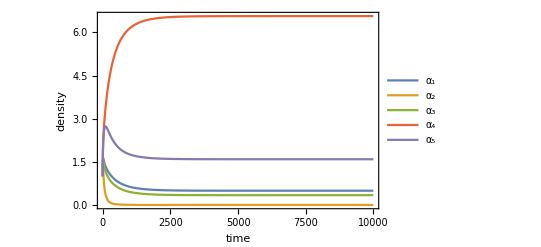

```mathematica
Plot[Evaluate[Table[Indexed[n[t],a]/.sols,{a,m}]],{t,0,10000},PlotRange->{All,{0,All}},Frame->True,FrameLabel->{"time","density"},PlotLegends->{"α_1","α_2","α_3","α_4","α_5"}]
```

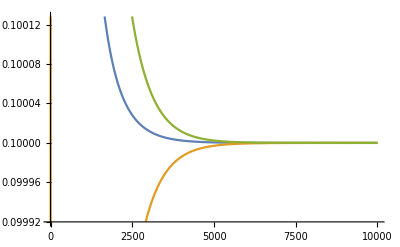

```mathematica
Plot[Evaluate[Table[Indexed[r[t],j]/.sols,{j,p}]],{t,0,10000}]
```

### Equilibrium state

```mathematica
crSteadyState[{n0_,c_,g_,z_},r0_,κ_,μ_,tMax_:10000]:=
NDSolveValue[{
r[0]==r0,
r'[t]==κ-μ*r[t]-r[t]*n[t].c,
n[0]==n0,
n'[t]==n[t]*(r[t].Transpose[c*g]-z)
},
n,
{t,0,tMax}][tMax]
```

```mathematica
crSteadyState[{n0,c,g,z},r0,κ,μ,10000]
```

{0.344008,1.70589×10^-13,8.65599,-3.84148×10^-22,-4.858×10^-15}

## HGT

Mutate one of the vectors and change all the corresponding vectors

```mathematica
mutateHGTOneStep[{n0_,c0_,g0_,z0_}]:=
	Module[{n=n0,c=c0,g=g0,z=z0,p=Length[c[[1]]],mutation,h},
	(*mutation*)
		mutation=Table[RandomVariate[UniformDistribution[{1,1.03}]],p];
		AppendTo[c,enzymeBudget*Normalize[Ramp[RandomChoice[Ramp[n]->c]*mutation],Total]];
		AppendTo[n,0.001*Total[n]];
		AppendTo[g,Table[1,p]];
		AppendTo[z,0.1];
		n=Chop[crSteadyState[{n,c,g,z},r0,κ,μ],10^-6];
		(*create h, probability of gene transfer from the newly mutated individual
		(works because it's always last index)*)
		h=Append[Table[(n[[i]]*n[[-1]])/Total[n],{i,1,(Length[n]-1)}],0];
		(*horizontal gene transfer*)
		Do[
			If[RandomReal[]<h[[i]],
				c[[i]] = Normalize[Ramp[c[[i]]*mutation],Total]
			],
			{i,Length[n]}
		];
		n=Ramp[Chop[crSteadyState[{n,c,g,z},r0,κ,μ],10^-6]];
		{n,c,g,z}=Delete[#,Position[n,0]]&/@{n,c,g,z};
		{n,c,g,z}
	]
```

```mathematica
exampleState={{0.34189001677926056,0,8.652347333496376,0,0,0.005762650114975366},{{0.5209537510080495,0.18877123036426002,0.29027501862769045},{0.4406625778464477,0.3945143920395882,0.16482303011396413},{0.3564363622708176,0.3633197672656839,0.2802438704634985},{0.6080243168086128,0.35134510593384044,0.04063057725754676},{0.18504133408656218,0.7231374755118568,0.09182119040158097},{0.3582213656076538,0.3653179180762353,0.27646071631611085}},{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1}},{0.1,0.1,0.1,0.1,0.1,0.1}};
```

```mathematica
Delete[#,Position[exampleState[[1]],0]]&/@exampleState
```

{{0.34189,8.65235,0.00576265},{{0.520954,0.188771,0.290275},{0.356436,0.36332,0.280244},{0.358221,0.365318,0.276461}},{{1,1,1},{1,1,1},{1,1,1}},{0.1,0.1,0.1}}

```mathematica
mutateHGTOneStep[{n0,c,g,z}]
```

{{8.48809,0.511729,0.000182672},{{0.28443,0.350706,0.364864},{0.424521,0.0370802,0.538398},{0.421228,0.0367588,0.542013}},{{1,1,1},{1,1,1},{1,1,1}},{0.1,0.1,0.1}}

```mathematica
Dynamic[track]
```

```mathematica
track=0;
runHGT=NestList[(track++;mutateHGTOneStep[#])&,{n0,c,g,z},300];
```

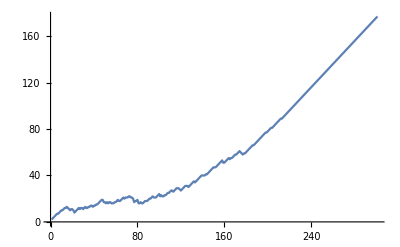

```mathematica
ListLinePlot[Length[#]-Count[#,0]&/@runHGT[[All,1]]]
```

```mathematica
BarChart[DeleteCases[runHGT[[-1,1]],0]]
```

```mathematica
runMultipleHGT50Initial4=Module[{c,runMultipleHGT},
	track=0;
	runMultipleHGT={};
	Do[AppendTo[runMultipleHGT,
		NestList[(c=enzymeBudget*Normalize[#,Total]&/@RandomReal[{0,1},{m,p}];
			track++;
			mutateHGTOneStep[#])&,{n0,c,g,z},300]],50];
	runMultipleHGT];
```

$Aborted

```mathematica
Export["/Users/katjad/Documents/Github/HGT/data/runMulitpleHGT50Initial4.mx",runMultipleHGT50Initial4];
```

```mathematica
Export["/Users/katjad/Documents/Github/HGT/data/runMulitpleHGT100.mx",runMultipleHGT100];
```

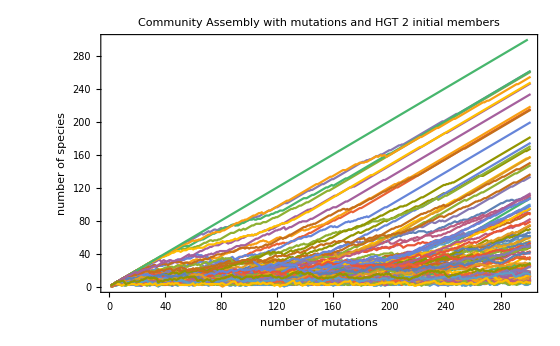

```mathematica
ListLinePlot[Function[n,Length[#]-Count[#,0]&/@n[[All,1]]]/@runMultipleHGT100,PlotRange->{{0,300},{0,300}},Frame->True,FrameLabel->{Style["number of mutations",18],Style["number of species",18]},PlotLabel->Style["Community Assembly with mutations and HGT\n 2 initial members",22]]
```

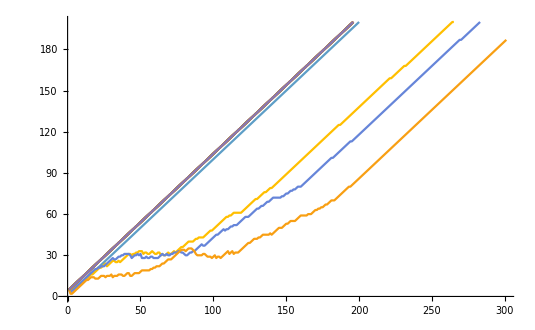

```mathematica
ListLinePlot[Function[n,Length[#]-Count[#,0]&/@n[[All,1]]]/@Join[runMultipleHGT,runMultipleHGT2],PlotRange->{{0,300},{0,200}}(*,PlotLegends->Table[n,{n,1,Length[Join[runMultipleHGT,runMultipleHGT2]]}]*)]
```

```mathematica
initialEndPlot[data_]:=Multicolumn[Show[ternaryPlot[data[[#,-1,2]]],Graphics[{Red,Point[data[[#,1,2]].CirclePoints[3]]}]]&/@sample,3]
```

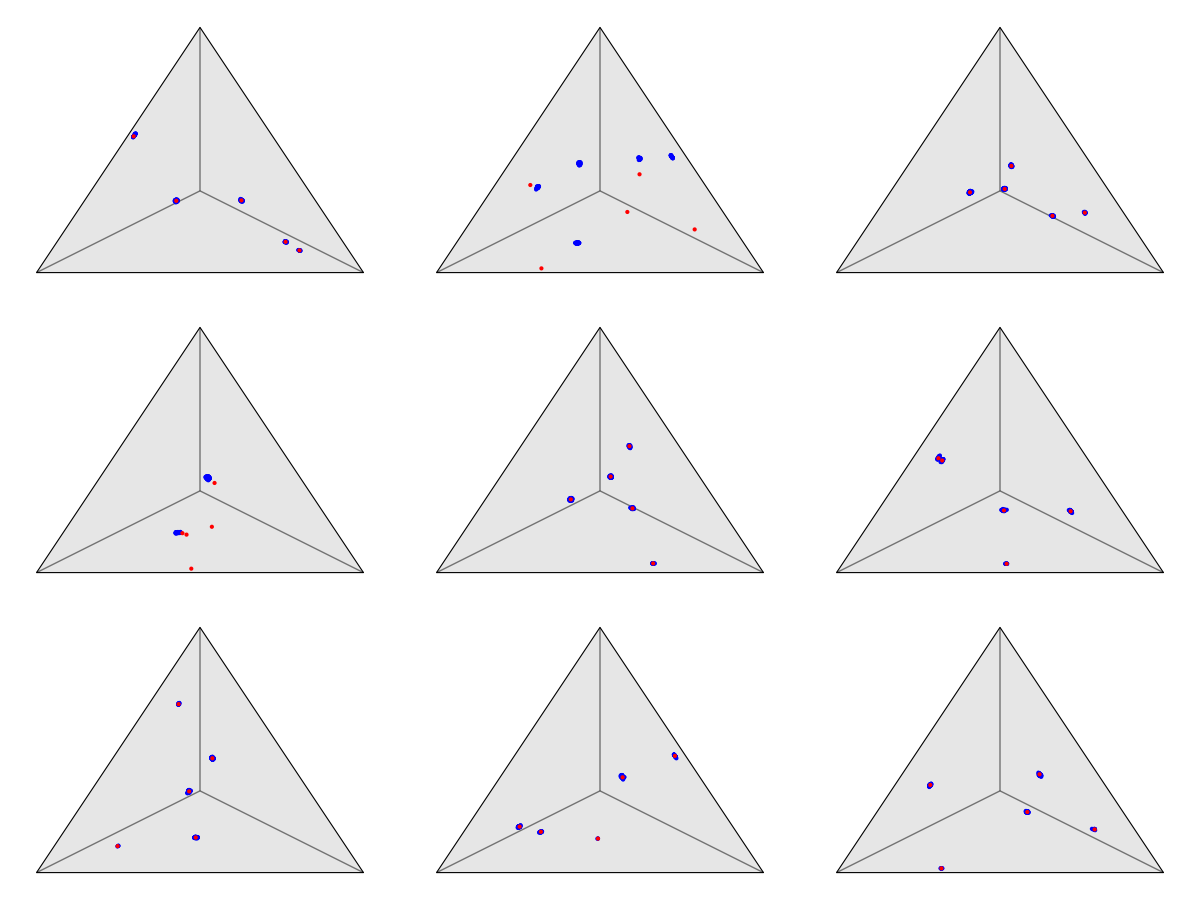

```mathematica
Multicolumn[Show[ternaryPlot[runMultipleHGT[[#,-1,2]]],Graphics[{Red,Point[runMultipleHGT[[#,1,2]].CirclePoints[3]]}]]&/@RandomSample[Range[10],9],3]
```

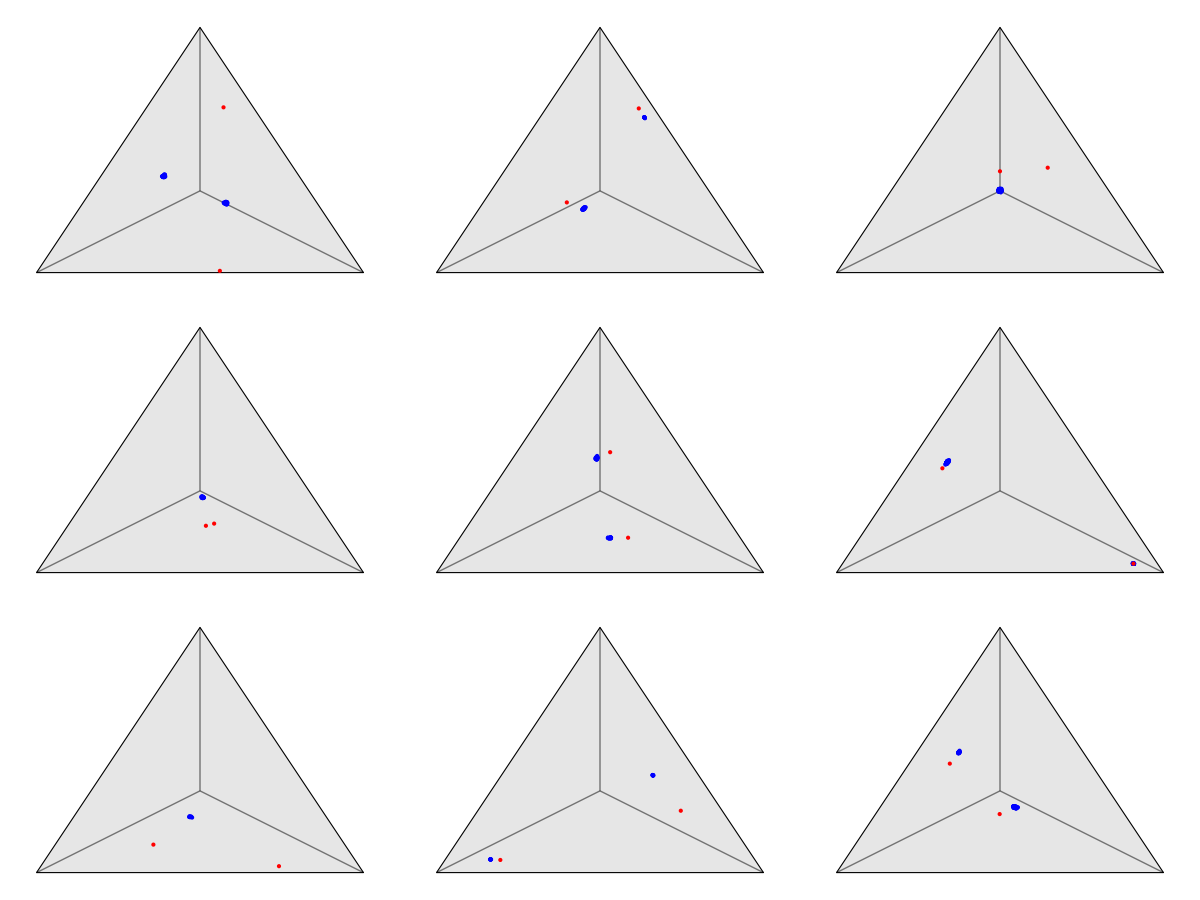

```mathematica
initialEndPlot[runMultipleHGT100]
```

## Repeated mutation and equilibrium

```mathematica
(*Input: each of the variables involving α 
Output: each of the updated variables*)
```

```mathematica
mutate[{n0_,c0_,g0_,z0_}]:=
	Module[{n=n0,c=c0,g=g0,z=z0,p=Length[c[[1]]],mutation},
		mutation=Table[RandomVariate[UniformDistribution[{1,1.03}]],p];
		AppendTo[c,enzymeBudget*Normalize[Ramp[RandomChoice[Ramp[n]->c]*mutation],Total]];
		AppendTo[n,0.001*Total[n]];
		AppendTo[g,Table[1,p]];
		AppendTo[z,0.1];
		{n,c,g,z}
	]
```

```mathematica
mutate[{n0,c,g,z}]
```

{{1,1,1,1,1,2},{{0.491571,0.403744,0.104685},{0.153196,0.797863,0.0489411},{0.511719,0.419206,0.0690746},{0.370881,0.291886,0.337233},{0.0909375,0.462768,0.446295},{0.492686,0.404685,0.102628}},{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1}},{0.1,0.1,0.1,0.1,0.1,0.1}}

```mathematica
oneStep[{n0_,c0_,g0_,z0_}]:=
	Module[{n=n0,c=c0,g=g0,z=z0},
		{n,c,g,z}=mutate[{n,c,g,z}];
		n=Ramp[Chop[crSteadyState[{n,c,g,z},r0,κ,μ],10^-6]];
		{n,c,g,z}=Delete[#,Position[n,0]]&/@{n,c,g,z};
		{n,c,g,z}]
```

```mathematica
runMultiple100=Module[{c,runMultiple},
	track=0;
	runMultiple={};
	Do[AppendTo[runMultiple,
		NestList[(c=enzymeBudget*Normalize[#,Total]&/@RandomReal[{0,1},{m,p}];
			track++;
			oneStep[#])&,{n0,c,g,z},300]],100];
	runMultiple];
```

```mathematica
Export["/Users/katjad/Documents/Github/HGT/data/runMulitple100.mx",runMultiple100]
```

/Users/katjad/Documents/Github/HGT/data/runMulitple100.mx

```mathematica
run=NestList[oneStep,{n0,c,g,z},100];
```

```mathematica
overTime=Length[#]-Count[#,0]&/@Chop[run[[All,1]]]
```

{5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105}

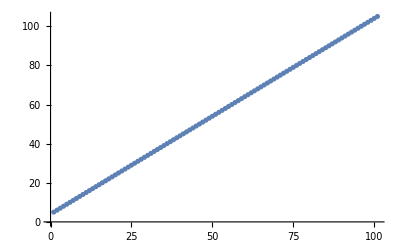

```mathematica
ListPlot[overTime]
```

```mathematica
sample=RandomSample[Range[100],9];
```

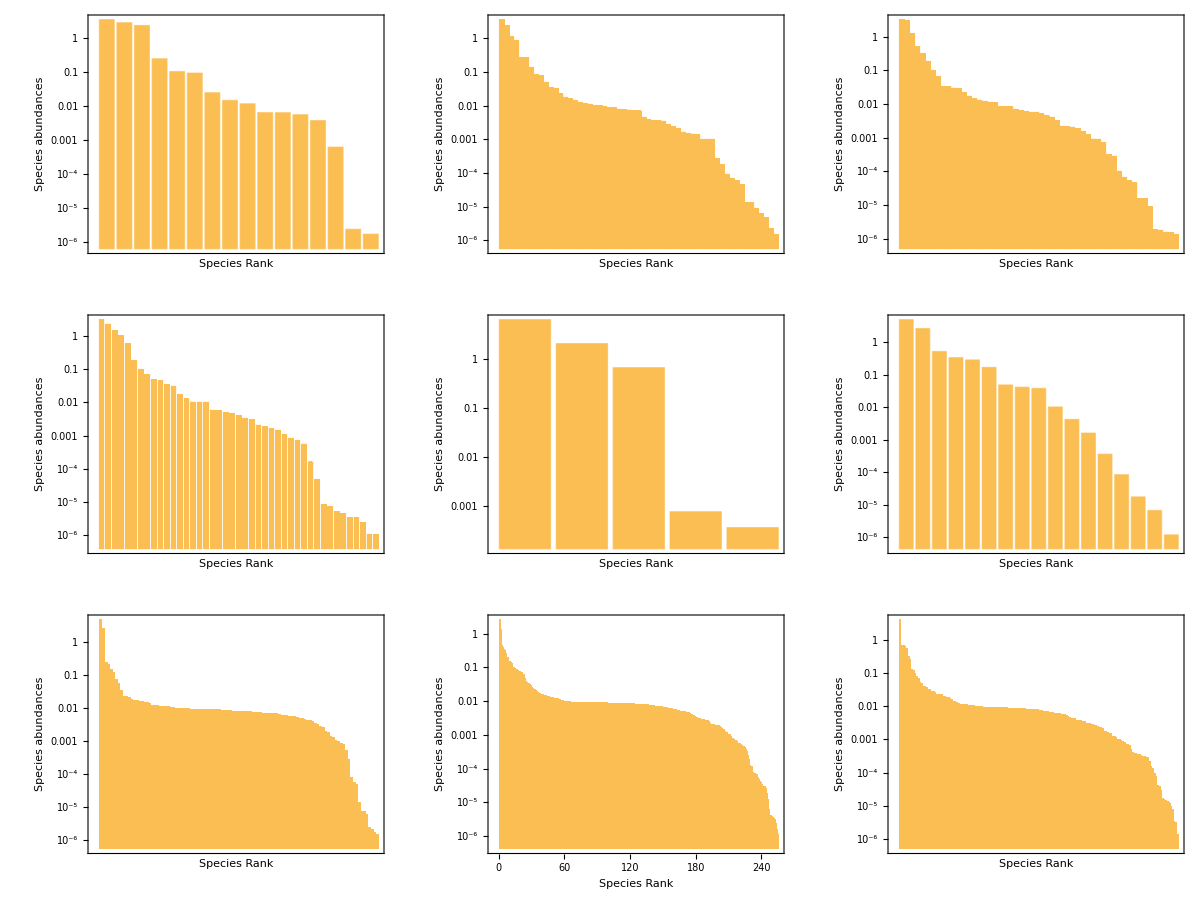

```mathematica
Multicolumn[BarChart[ReverseSort[runMultipleHGT100[[#,-1,1]]],Frame->True,ScalingFunctions->"Log",FrameLabel->{Style["Species Rank",10],Style["Species abundances",10]}]&/@sample,3]
```

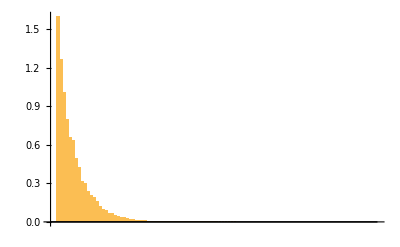

```mathematica
BarChart[ReverseSort[run[[-1,1]]]]
```

```mathematica
ternaryPlot[l_]:=Graphics[{{FaceForm[GrayLevel[0.9]],EdgeForm[Black],RegularPolygon[3]},{Opacity[0.5],Thin,Line[{{0,0},#}]&/@CirclePoints[3]},Blue,Point[l.CirclePoints[3]]}]
```

```mathematica
ternaryPlotRed[l_]:=Graphics[{{FaceForm[GrayLevel[0.9]],EdgeForm[Black],RegularPolygon[3]},{Opacity[0.5],Thin,Line[{{0,0},#}]&/@CirclePoints[3]},Red,Point[l.CirclePoints[3]]}]
```

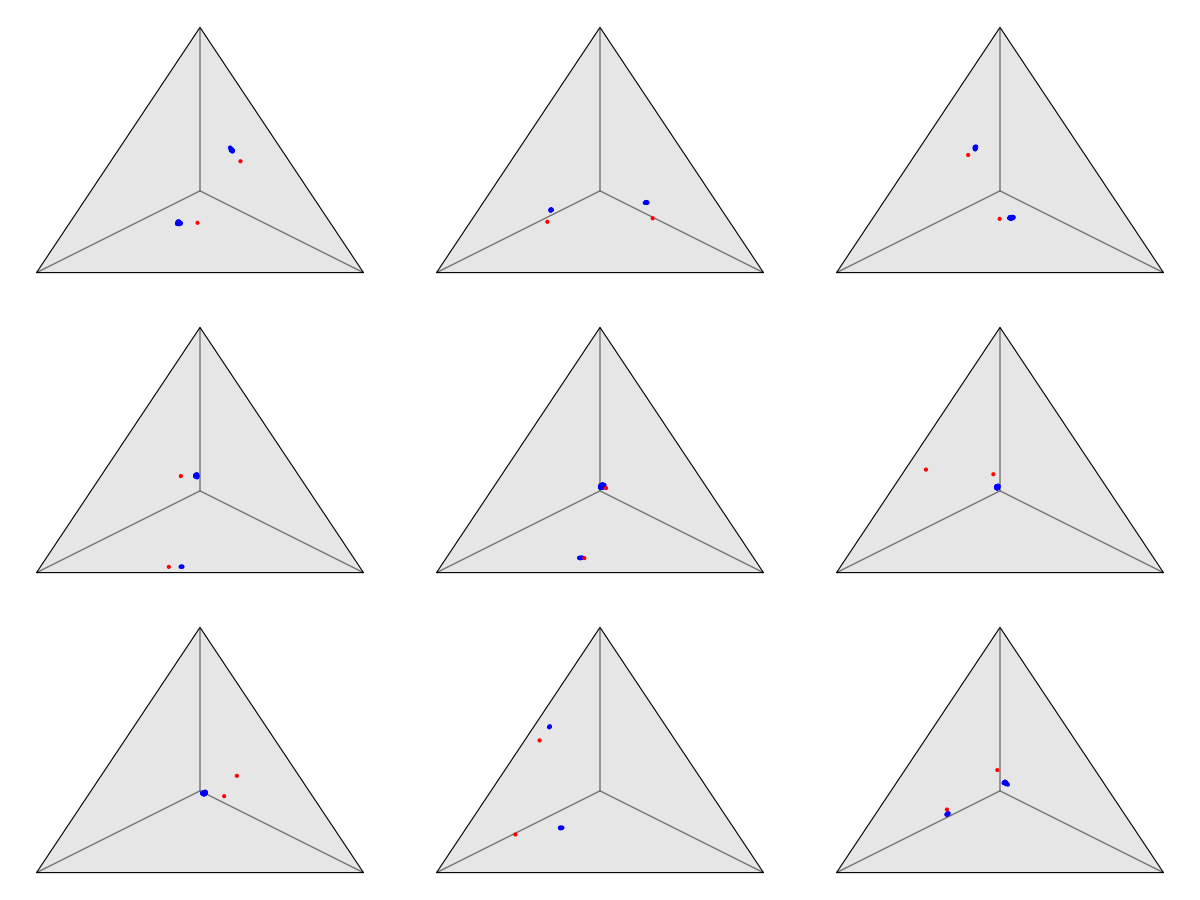

```mathematica
initialEndPlot[runMultiple100]
```

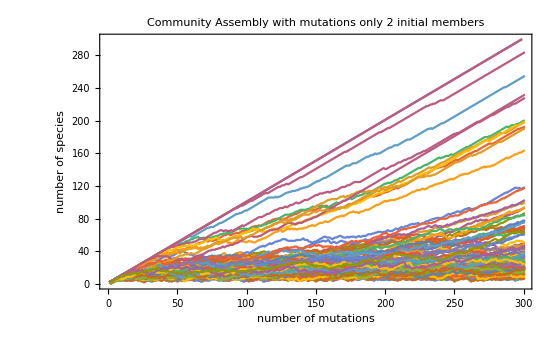

```mathematica
ListLinePlot[Function[n,Length[#]-Count[#,0]&/@n[[All,1]]]/@runMultiple100,PlotRange->{{0,300},{0,300}},Frame->True,FrameLabel->{Style["number of mutations",18],Style["number of species",18]},PlotLabel->Style["Community Assembly with mutations only\n 2 initial members",22]]
```